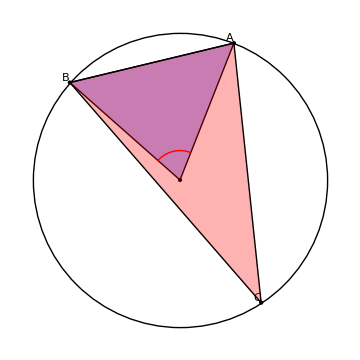

```mathematica
(* PIANO B con GRAPHICS*)
center = {0,0};
circle =Circle[center, 1];

startAngle = RandomReal[{0, Pi}]; 
circAngle = RandomReal[{alpha + 0.1, 2*Pi - 0.1 }];
alpha = 70°; (*ampiezza angolo al centro*)

p = CirclePoints[{1, startAngle}, 1][[1]];
p1 = RotationMatrix[alpha].p;

(*p3 = RotationMatrix[RandomReal[{alpha + 0.1, 2*Pi - 0.1 }]].p;(* punto corrispondente sulla circonferenza *) *)
p3 = RotationMatrix[circAngle].p;
(*
p4 = CirclePoints[{1, 2*Pi -0.1 + alpha }, 1][[1]];
p3 = CirclePoints[{1, RandomReal[{startAngle + alpha + 0.1  , 2*Pi -0.1 }]}, 1][[1]];
*)

Graphics[{circle, 
Point[center],Point[p],Point [p1], Point[p3],
{Opacity[0.3],Style[Triangle[{p,p1,center}], Blue]},
Line[{p,p1,center, p}],
{Opacity[0.3],Style[Triangle[{p,p1,p3}], Red]},
Line[{p,p1,p3, p}],
Style[Circle[center, 0.2, {startAngle, startAngle + alpha}], Red, Thick ],
Text[A, p, {1.5,-1.5} ],
Text[B, p1, {1.5,-1.5} ],
Text[C, p3, {1.5,-1.5} ]
}, ImageSize -> Medium]
```